```mathematica
filenames={"Table_Stochastic_control3_selfing1_sexualReproduction1_seedbank1_cost1_kCost5_kHerb5_fieldsize10000.txt",
"Table_Stochastic_control3_selfing1_sexualReproduction1_seedbank1_cost300_kCost5_kHerb5_fieldsize10000.txt"};
```

```mathematica
data=Table[Import[NotebookDirectory[]<>"../data/"<>filenames⟦i⟧,"CSV"],{i,1,2,1}];
```

## File 1

```mathematica
gatherruns=GatherBy[data⟦1,2;;,{1,5,2}⟧,Last];
```

```mathematica
runs=Partition[data⟦1,2;;,5⟧,30];
```

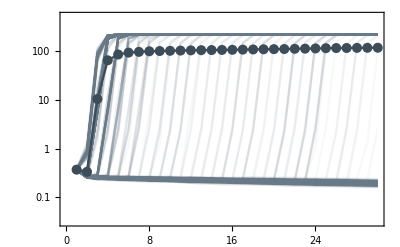

```mathematica
Show[ListLogPlot[Table[gatherruns⟦i⟧⟦All,2⟧,{i,1,1000,1}],Joined->True,PlotRange->{Automatic,{10^-1.5,10^2.7}},PlotStyle->Directive[Opacity[0.05],RGBColor["#687988"]],Joined->True,Frame->True,FrameStyle->Directive[Black,Thickness[0.005]],FrameLabel->None],
ListLogPlot[gatherruns⟦1001⟧⟦All,2⟧,Joined->True,Mesh->True,MeshStyle->PointSize[0.018],PlotStyle->Directive[Full,RGBColor["#3C4C59"]],Joined->True,Frame->True,FrameStyle->Directive[Black,Thickness[0.005]],FrameLabel->None]]
```

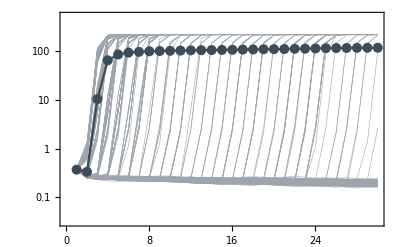

```mathematica
Show[ListLogPlot[Table[gatherruns⟦i⟧⟦All,2⟧,{i,1,1000,1}],Joined->True,PlotRange->{Automatic,{10^-1.5,10^2.7}},PlotStyle->Directive[Lighter[RGBColor["#3C4C59"],0.5],Thickness[0.001]],Joined->True,Frame->True,FrameStyle->Directive[Black,Thickness[0.005]],FrameLabel->None],
ListLogPlot[gatherruns⟦1001⟧⟦All,2⟧,Joined->True,Mesh->True,MeshStyle->PointSize[0.018],PlotStyle->Directive[Full,RGBColor["#3C4C59"]],Joined->True,Frame->True,FrameStyle->Directive[Black,Thickness[0.005]],FrameLabel->None]]
```

```mathematica
{rwcol,rrcol,wwcol}={RGBColor["#F2A35E"],RGBColor["#BF766F"],RGBColor["#7C92A6"]}
```

{RGBColor[0.9490196078431372, 0.6392156862745098, 0.3686274509803922],RGBColor[0.7490196078431373, 0.4627450980392157, 0.43529411764705883],RGBColor[0.48627450980392156, 0.5725490196078431, 0.6509803921568628]}

```mathematica
gatherrunscol=GatherBy[data⟦1,2;;,{1,6,7,8,2}⟧,Last];
```

```mathematica
tab=Table[Transpose[gatherrunscol⟦i⟧⟦All,{2,3,4}⟧/10^4],{i,1,1001,1}];
```

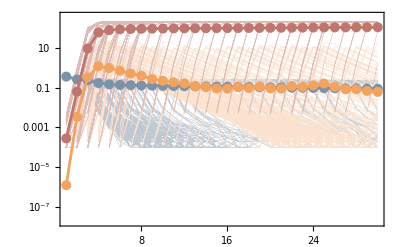

```mathematica
Show[ListLogPlot[tab⟦1;;1000,1⟧,PlotStyle->Directive[Lighter[wwcol,0.5],Thickness[0.001]],Joined->True,Frame->True,FrameStyle->Directive[Black,Thickness[0.005]],FrameLabel->None],
ListLogPlot[tab⟦1;;1000,2⟧,PlotStyle->Directive[Lighter[rwcol,0.7],Thickness[0.001]],Joined->True,Frame->True,FrameStyle->Directive[Black,Thickness[0.005]],FrameLabel->None],
ListLogPlot[tab⟦1;;1000,3⟧,PlotStyle->Directive[Lighter[rrcol,0.5],Thickness[0.001]],Joined->True,Frame->True,FrameStyle->Directive[Black,Thickness[0.005]],FrameLabel->None],
ListLogPlot[tab⟦1001,1⟧,Mesh->True,MeshStyle->PointSize[0.018],PlotStyle->Directive[wwcol,Thickness[0.005]],Joined->True,Frame->True,FrameStyle->Directive[Black,Thickness[0.005]],FrameLabel->None],
ListLogPlot[tab⟦1001,2⟧,Mesh->True,MeshStyle->PointSize[0.018],PlotStyle->Directive[Darker[rwcol,0.00],Thickness[0.005]],Joined->True,Frame->True,FrameStyle->Directive[Black,Thickness[0.005]],FrameLabel->None],
ListLogPlot[tab⟦1001,3⟧,Mesh->True,MeshStyle->PointSize[0.018],PlotStyle->Directive[rrcol,Thickness[0.005]],Joined->True,Frame->True,FrameStyle->Directive[Black,Thickness[0.005]],FrameLabel->None],
PlotRange->{Automatic,{-17.9,6}},Axes->None]
```

## File 2

```mathematica
gatherruns=GatherBy[data⟦2,2;;,{1,5,2}⟧,Last];
```

```mathematica
runs=Partition[data⟦2,2;;,5⟧,30];
```

```mathematica
Show[ListLogPlot[Table[gatherruns⟦i⟧⟦All,2⟧,{i,1,1000,1}],Joined->True,PlotRange->{Automatic,{10^-1.5,10^2.7}},PlotStyle->Directive[Opacity[0.05],RGBColor["#687988"]],Joined->True,Frame->True,FrameStyle->Directive[Black,Thickness[0.005]],FrameLabel->None],
ListLogPlot[gatherruns⟦1001⟧⟦All,2⟧,Joined->True,Mesh->True,MeshStyle->PointSize[0.018],PlotStyle->Directive[Full,RGBColor["#3C4C59"]],Joined->True,Frame->True,FrameStyle->Directive[Black,Thickness[0.005]],FrameLabel->None]]
```

-Graphics-

```mathematica
Show[ListLogPlot[Table[gatherruns⟦i⟧⟦All,2⟧,{i,1,1000,1}],Joined->True,PlotRange->{Automatic,{10^-1.5,10^2.7}},PlotStyle->Directive[Lighter[RGBColor["#3C4C59"],0.5],Thickness[0.001]],Joined->True,Frame->True,FrameStyle->Directive[Black,Thickness[0.005]],FrameLabel->None],
ListLogPlot[gatherruns⟦1001⟧⟦All,2⟧,Joined->True,Mesh->True,MeshStyle->PointSize[0.018],PlotStyle->Directive[Full,RGBColor["#3C4C59"]],Joined->True,Frame->True,FrameStyle->Directive[Black,Thickness[0.005]],FrameLabel->None]]
```

-Graphics-

```mathematica
{rwcol,rrcol,wwcol}={RGBColor["#F2A35E"],RGBColor["#BF766F"],RGBColor["#7C92A6"]}
```

{RGBColor[0.9490196078431372, 0.6392156862745098, 0.3686274509803922],RGBColor[0.7490196078431373, 0.4627450980392157, 0.43529411764705883],RGBColor[0.48627450980392156, 0.5725490196078431, 0.6509803921568628]}

```mathematica
gatherrunscol=GatherBy[data⟦2,2;;,{1,6,7,8,2}⟧,Last];
```

```mathematica
tab=Table[Transpose[gatherrunscol⟦i⟧⟦All,{2,3,4}⟧/10^4],{i,1,1001,1}];
```

```mathematica
Show[ListLogPlot[tab⟦1;;1000,1⟧,PlotStyle->Directive[Lighter[wwcol,0.5],Thickness[0.001]],Joined->True,Frame->True,FrameStyle->Directive[Black,Thickness[0.005]],FrameLabel->None],
ListLogPlot[tab⟦1;;1000,2⟧,PlotStyle->Directive[Lighter[rwcol,0.7],Thickness[0.001]],Joined->True,Frame->True,FrameStyle->Directive[Black,Thickness[0.005]],FrameLabel->None],
ListLogPlot[tab⟦1;;1000,3⟧,PlotStyle->Directive[Lighter[rrcol,0.5],Thickness[0.001]],Joined->True,Frame->True,FrameStyle->Directive[Black,Thickness[0.005]],FrameLabel->None],
ListLogPlot[tab⟦1001,1⟧,Mesh->True,MeshStyle->PointSize[0.018],PlotStyle->Directive[wwcol,Thickness[0.005]],Joined->True,Frame->True,FrameStyle->Directive[Black,Thickness[0.005]],FrameLabel->None],
ListLogPlot[tab⟦1001,2⟧,Mesh->True,MeshStyle->PointSize[0.018],PlotStyle->Directive[Darker[rwcol,0.00],Thickness[0.005]],Joined->True,Frame->True,FrameStyle->Directive[Black,Thickness[0.005]],FrameLabel->None],
ListLogPlot[tab⟦1001,3⟧,Mesh->True,MeshStyle->PointSize[0.018],PlotStyle->Directive[rrcol,Thickness[0.005]],Joined->True,Frame->True,FrameStyle->Directive[Black,Thickness[0.005]],FrameLabel->None],
PlotRange->{Automatic,{-17.9,6}},Axes->None]
```

-Graphics-

## HistoGram Plots

```mathematica
histodata=Import[NotebookDirectory[]<>"../data/"<>"Table_EscapeYearDistribution_cost.txt","CSV"];
```

```mathematica
histodata⟦2;;⟧⟦1;;-2,1⟧
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30}

```mathematica
topl={histodata⟦2;;⟧⟦1;;-2,2⟧,histodata⟦2;;⟧⟦1;;-2,3⟧}(*/.{0->"10^-10"}*)
```

{{332,69,26,13,10,9,3,4,6,6,2,3,3,3,5,3,5,2,3,6,3,6,6,2,2,3,2,0,2,5},{0,1,10,7,7,10,6,7,11,11,7,8,11,10,10,5,11,9,12,10,6,8,10,3,11,8,4,4,7,6}}

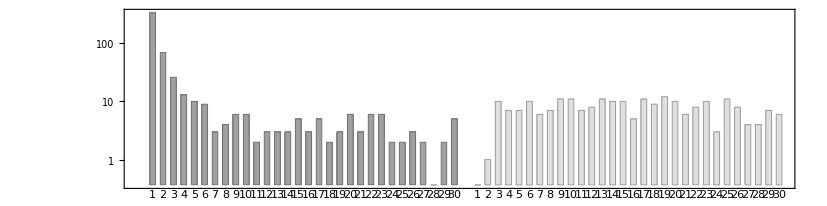

```mathematica
BarChart[topl,ScalingFunctions->"Log",AspectRatio->0.25,ChartStyle->{{Directive[EdgeForm[Black], Gray,Opacity[0.75]],Directive[EdgeForm[Black], Gray,Opacity[0.25]]},None},Frame->True,ChartLabels->{None,Placed[histodata⟦2;;⟧⟦1;;-2,1⟧,Below]},BarSpacing->{0.8,3},FrameStyle->Directive[Black,Thickness[0.002]]]
```

```mathematica
{histodata⟦2;;⟧⟦-1,2⟧,1000-histodata⟦2;;⟧⟦-1,2⟧}/1000//N
```

{0.456,0.544}

```mathematica
PieChart[{1000-histodata⟦2;;⟧⟦-1,2⟧,histodata⟦2;;⟧⟦-1,2⟧}/1000,ChartStyle->{Directive[ Gray,Opacity[0.75]],White},ChartLabels->Placed[{Style["54.4% escapes",24,Black],},"RadialCallout"],ImageSize->Medium,ImagePadding->{{None,30},{-10,-10}}]
```

-Graphics-

```mathematica
PieChart[{1000-histodata⟦2;;⟧⟦-1,3⟧,histodata⟦2;;⟧⟦-1,3⟧}/1000,ChartStyle->{Directive[ Gray,Opacity[0.25]],White},ChartLabels->Placed[{Style["23% escapes",24,Black],},"RadialCallout"],ImageSize->Medium,ImagePadding->{{100,None},{-10,-10}}]
```

-Graphics-